```mathematica
Sum[i^2,{i,0,M-1}]
```

1/6 (-1+M) M (-1+2 M)

```mathematica
p=Hold[1/m Sum[1/(σ √(2π))E^(-(y-i)^2/(2 σ^2)),{i,0,m-1}]]
```

Hold[(∑_(i=0)^(m-1) (ⅇ^(-(y-i)^2/(2 σ^2)))/(σ √(2 π)))/m]

```mathematica
ReleaseHold[p]
```

1/2 ((ⅇ^(-(-1+y)^2/(2 σ^2)))/(√(2 π) σ)+(ⅇ^(-y^2/(2 σ^2)))/(√(2 π) σ))

```mathematica
m=4
σ=√(((2-1)(4-1))/(6 10^sn))
p=1/m Sum[1/(σ √(2π))E^(-(y-i)^2/(2 σ^2)),{i,0,m-1}]
```

4

√(2^(-1-sn) 5^-sn)

1/4 ((ⅇ^(-10^sn (-3+y)^2))/(√(2^(-1-sn) 5^-sn) √(2 π))+(ⅇ^(-10^sn (-2+y)^2))/(√(2^(-1-sn) 5^-sn) √(2 π))+(ⅇ^(-10^sn (-1+y)^2))/(√(2^(-1-sn) 5^-sn) √(2 π))+(ⅇ^(-10^sn y^2))/(√(2^(-1-sn) 5^-sn) √(2 π)))

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {2.96924}. NIntegrate obtained 2.70921 and 0.00155096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.00006}. NIntegrate obtained 2.37886 and 0.000182021 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^-10^sn\ (-3 + y)^2/√2^-1 + Times[« 2 »]\ 5^-sn\ √2\ π + ⅇ^-10^sn\ « 1 »^2/√2^-1 « 1 » Times « 1 » « 1 »]\ 5^-sn\ √2\ π + ⅇ^-« 1 »\ « 1 »/√2^« 1 »\ 5^« 1 »\ √2\ π + ⅇ^-10^sn\ y^2/√2^-1 + Times[« 2 »]\ 5^-sn\ √2\ π)\ Log[1/4\ (« 1 »/« 1 » + « 2 » + « 1 »)]/4\ Log[2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

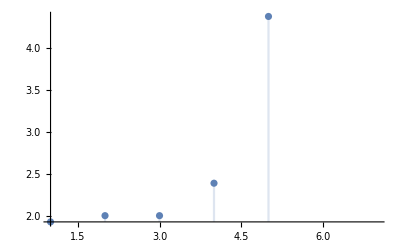

```mathematica
DiscretePlot[-NIntegrate[p Log2[p],{y,-Infinity,Infinity}]-Log2[σ √(2π E)],{sn,{1,2,3,4,5,6,7}}]
```

```mathematica
p
```

1/2 ((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn)))

```mathematica
-NIntegrate[(((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn))) Log[1/2 ((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn)))])/(2 Log[2]),{y,-Infinity,Infinity}]-Log2[σ √(2π E)]
```

NIntegrate::inumr: The integrand (ⅇ^-sn\ (-1 + y)^2/√π\ √1/sn + ⅇ^-sn\ y^2/√π\ √1/sn)\ Log[1/2\ (ⅇ^-sn\ Power[« 2 »]/√π\ √1/sn + ⅇ^-sn\ Power[« 2 »]/√π\ √1/sn)]/2\ Log[2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

-Log[√(ⅇ π) √(1/sn)]/Log[2]-NIntegrate[(((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn))) Log[1/2 ((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn)))])/(2 Log[2]),{y,-∞,∞}]

```mathematica
p Log2[p]
```

(((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn))) Log[1/2 ((ⅇ^(-sn (-1+y)^2))/(√π √(1/sn))+(ⅇ^(-sn y^2))/(√π √(1/sn)))])/(2 Log[2])